```mathematica
pathtoMATCHApackage="/home/carlos/MATCHA-release-main"
```

/home/carlos/MATCHA-release-main

```mathematica
pathtoexport="/home/carlos/MATCHA-release-main"
```

/home/carlos/MATCHA-release-main

# MATCHA

```mathematica
SetDirectory[pathtoMATCHApackage]
```

/home/carlos/MATCHA-release-main

```mathematica
<<MATCHA`
```

==============================================

MATCHA

MATChing H(EFT) Amplitudes

by Raquel Gómez-Ambrosio and Carlos Quezada Calonge

Version: MATCHA 1.0

=============================================

-Graphics-

```mathematica
LoadTools[];
```

Loading FeynArts...

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

Loading FormCalc...

FormCalc 9.8 (22 Apr 2019)

by Thomas Hahn

Tools loaded successfully.

```mathematica
Options[MatchToHEFT]
```

{EFTorder→2,SimplifyResult→True,ExportDiagrams→False,OutputDirectory→Automatic,AlternativeBasis→True,OnlyRelevantDiagrams→False}

# Definitions

```mathematica
?SetSMFields
```

```mathematica
?SetSMParams
```

```mathematica
?SetBSMFields
```

```mathematica
?MatchToHEFT
```

# Real Singlet Extension

```mathematica
SetSMFields[<|"Higgs"->{"S",15},"GaugeCharged"->{"V",2},"GoldstoneCharged"->{"S",5},"GoldstoneNeutral"->{"S",3},"Quark"->{"F",1}|>]
```

SM fields set to: <|Higgs→S(15),GaugeCharged→V(2),GoldstoneCharged→S(5),GoldstoneNeutral→S(3),Quark→F(1)|>

<|Higgs→S(15),GaugeCharged→V(2),GoldstoneCharged→S(5),GoldstoneNeutral→S(3),Quark→F(1)|>

```mathematica
SetSMParams[<|"HiggsMass"->m,"SMvacuum"->v,"WMass"->Mw,"QuarkMass"->Mt|>]
```

SM parameters set to: <|HiggsMass→m,SMvacuum→v,WMass→Mw,QuarkMass→Mt|>

<|HiggsMass→m,SMvacuum→v,WMass→Mw,QuarkMass→Mt|>

```mathematica
SetBSMFields[{{"S",6}}]
```

BSM fields set to: {S(6)}

{S(6)}

```mathematica
MatchToHEFT["Singlet_for_MATCHA",3,{M},ExportDiagrams->True,OnlyRelevantDiagrams->False,OutputDirectory-> pathtoexport]
```

MATCHA: Matching "Singlet_for_MATCHA" model onto HEFT

[1/7]  Generating UV diagrams ...

[2/7]  Generating UV amplitudes ...

[3/7]  Processing UV amplitudes ...

[4/7]  Expanding UV amplitudes ...

[5/7]  Rewriting kinematics ...

[6/7]  Solving ...

[7/7]  Obtaining HEFT couplings ...

HEFT coefficient | Matching Expression
d3 | c^3-(s^3 v)/vs
d4 | -(-3 c^6 vs^2+16 c^4 s^2 vs^2+38 c^3 s^3 v vs+16 c^2 s^4 v^2-3 s^6 v^2)/(3 vs^2)
d5 | (c^2 s^2 (c vs+s v)^2 (c^3 (-vs)-2 c^2 s v+2 c s^2 vs+s^3 v))/(2 vs^3)
a1 | (c e^2 v^2)/(2 Mw^2 SW2)
a2 | -(c e^2 v^2 (c s^2 vs-c vs+s^3 v))/(4 Mw^2 SW2 vs)
a3 | -(c^2 e^2 s^2 v^2 (c^3 vs^2+5 c^2 s v vs+c s^2 (4 v^2-3 vs^2)+3 c vs^2-3 s (s^2-1) v vs))/(12 Mw^2 SW2 vs^2)
c1 | c
c2 | -(c s^2 (c vs+s v))/(2 vs)
c3 | -(c^2 s^2 (c^3 vs^2+5 c^2 s v vs+c s^2 (4 v^2-3 vs^2)-3 s^3 v vs))/(6 vs^2)

## Diags

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

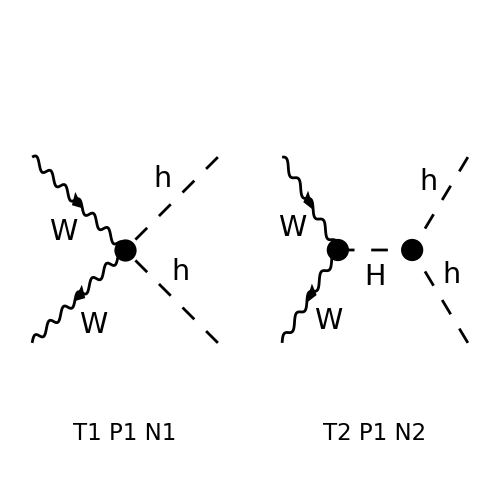

FeynArtsGraphics({W,W}→{h,h})(([T1 P1 N1] | [T2 P1 N2]))

```mathematica
Paint[MATCHADiagrams["a2"]["RelevantDiagrams"],ColumnsXRows->{2,1},ImageSize->500,ColumnsXRows->3]
```

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

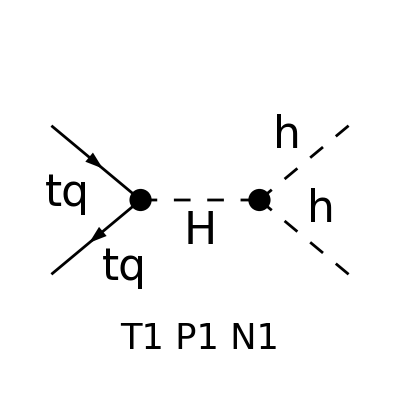

FeynArtsGraphics({tq,tq}→{h,h})(([T1 P1 N1]))

```mathematica
figc2=Paint[MATCHADiagrams["c2"]["RelevantDiagrams"],ColumnsXRows->{1,1},ImageSize->500,ColumnsXRows->3]
```

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

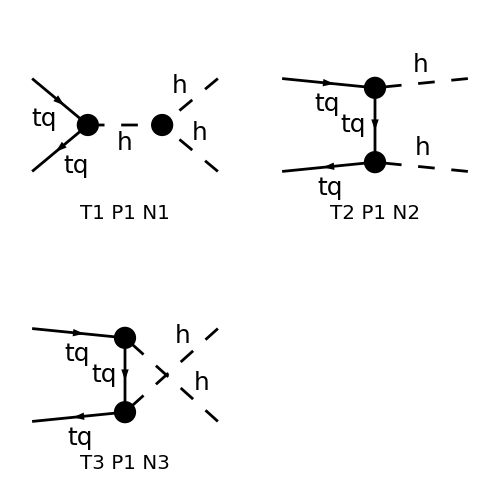

FeynArtsGraphics({tq,tq}→{h,h})(([T1 P1 N1] | [T2 P1 N2]
[T3 P1 N3] | Null))

```mathematica
figc2ignored=Paint[MATCHADiagrams["c2"]["IgnoredDiagrams"],ColumnsXRows->{2,2},ImageSize->500,ColumnsXRows->3]
```

> Top. 1 afbf/cgdgeg/fg.m, 0 diagrams

> Top. 2 afbf/cgdgeh/fhgh.m, 0 diagrams

> Top. 3 afbf/cgdheg/fhgh.m, 0 diagrams

> Top. 4 afbf/cgdheh/fggh.m, 0 diagrams

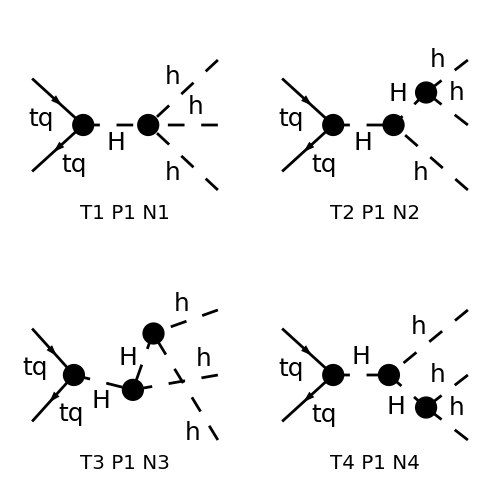

FeynArtsGraphics({tq,tq}→{h,h,h})(([T1 P1 N1] | [T2 P1 N2]
[T3 P1 N3] | [T4 P1 N4]))

```mathematica
figc3=Paint[MATCHADiagrams["c3"]["RelevantDiagrams"],ColumnsXRows->{2,2},ImageSize->500,ColumnsXRows->3]
```